```mathematica
<<PhysicalConstants`
<<Units`
```

General::obspkg: "PhysicalConstants`" is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

```mathematica
nc = Convert[VacuumPermittivity * ElectronMass *4 *π^2*SpeedOfLight^2/(ElectronCharge^2(1.057 *10^-6 Meter)^2),1*Centi^-3*Meter^-3]
```

(9.97857×10^20)/(Centi^3 Meter^3)

```mathematica
Convert[nc,1/(Centi Meter)^3]
```

(9.97857×10^20)/(Centi^3 Meter^3)

```mathematica
wpr = π/(150 Femto Second)
```

π/(150 Femto Second)

```mathematica
npr = Convert[wp^2*VacuumPermittivity ElectronMass/ElectronCharge^2,1/(Centi Meter)^3]
```

Convert::incomp: Incompatible units in 0.000314208\ Ampere\ Kilogram\ Second\ wp^2/Coulomb^2\ Meter\ Volt and 1/Centi^3\ Meter^3.

(0.000314208 Ampere Kilogram Second wp^2)/(Coulomb^2 Meter Volt)

```mathematica
wp = Convert[Sqrt[4.8*10^17(Centi Meter)^-3*ElectronCharge^2/(VacuumPermittivity*ElectronMass)],1/Second]
```

(3.90852×10^13)/Second

```mathematica
Ep = Convert[SpeedOfLight*ElectronMass*wp/ElectronCharge,Giga Volt/Meter]
```

(66.621 Giga Volt)/Meter

```mathematica
Ewb = Sqrt[2*(Sqrt[nc/(4.8*10^17 Centi^-3 Meter^-3)]-1)]Ep
```

(629.169 Giga Volt)/Meter

```mathematica
a0 = Sqrt[2*(Sqrt[nc/(4.8*10^17 Centi^-3 Meter^-3)]-1)]*Sqrt[2]
```

13.3558

```mathematica
wpf[ne_]:=(((1.67*10^-19)^2*ne)/(8.85*10^-12*9.11*10^-31))^(1/2);
wo[ne_,λ_]:= Sqrt[wpf[ne]^2+4*π^2*(3*10^8)^2/λ^2]
EzT[ne_,a_]:= Sqrt[ne]*Sqrt[a];
Ld[λ_,ne_,a_] := 4/3 3*10^8*(wo[ne,λ]^2*Sqrt[a])/wpf[ne]^3;
```

```mathematica
Lpd[λ_,ne_,τ_] :=3*10^8*(wo[ne,λ]^2*τ)/wpf[ne]^2;
Ldiff[a_,ne_,λ_ ]:= π*4*(a*(3*10^8)^2)/(λ*wpf[ne]^2);
```

```mathematica
Ldiff[8,4*10^23,1*10^-6]//N
```

0.006539

```mathematica
Lpd[1*10^-6,4*10^23,30*10^-15]//N
```

0.0231197

```mathematica
Ld[1*10^-6,4*10^23,8]
```

0.0781321

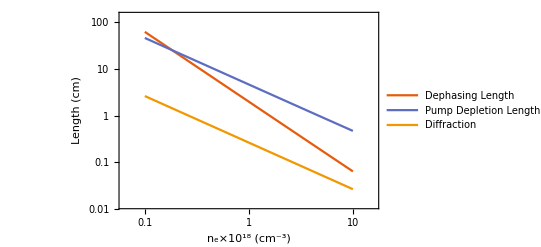

```mathematica
LogLogPlot[{Ld[1*10^-6,ne*10^24,8]/10^-2,Lpd[1*10^-6,ne*10^24,150*10^-15]/10^-2,Ldiff[8,ne*10^24,1*10^-6]/10^-2},{ne,.1,10},PlotLegends->{"Dephasing Length","Pump Depletion Length","Diffraction"},FrameLabel->{"n_e×10^18 (cm^-3)","Length (cm)"}, PlotTheme->"Scientific"]
```

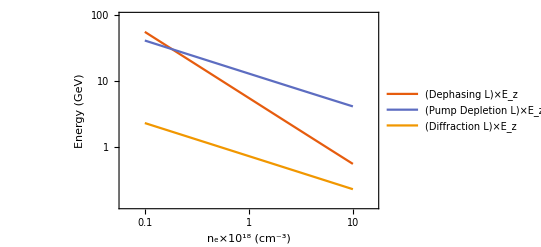

```mathematica
LogLogPlot[{Ld[1*10^-6,ne*10^24,8]/10^-2*Sqrt[8]*Sqrt[ne],Lpd[1*10^-6,ne*10^24,150*10^-15]*Sqrt[8]*Sqrt[ne]/10^-2,Ldiff[8,ne*10^24,1*10^-6]*Sqrt[8]*Sqrt[ne]/10^-2},{ne,.1,10},PlotLegends->{"(Dephasing L)×E_z","(Pump Depletion L)×E_z","(Diffraction L)×E_z"},FrameLabel->{"n_e×10^18 (cm^-3)","Energy (GeV)"}, PlotTheme->"Scientific"]
```

### Dispersion Graph

```mathematica
ω = Sqrt[
```